```mathematica
{y'(x)=-2 y,y(0)=1}
```

Set::write: Tag Times in x y' is Protected.

Set::write: Tag Times in 0 y is Protected.

{-2 y,1}

```mathematica
ParametricPlot[{-2 y,1},{x
,-1,1}]
```

-Graphics-

```mathematica
system={p'(x)==1,q'(x)==x,r'(x)==0,s'(x)==(r(x))/(p(x)+4 q(x) r(x))};
```

```mathematica
{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}
```

```mathematica
{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}
ⅇ^0
```

{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}

1

```mathematica
plot(sigm(x))

{
A=3.25*10^-3,
B=22*10^-3,
G=10*10^-3,
a=100,
b=50,
g=500,
C=135,
C1=C,
C2=0.8*C,
C3=0.25*C,
C4=0.25*C,
C5=0.3*C,
C6=0.1*C,
C7=0.8*C,
e0 = 2.5,
r=0.56*10^-3,
v0 = 6*10^-3,

S[u_]:=(2*e0)/(1+ⅇ^(r*(v0-u)))}
```

plot sigm x

{0.00325,11/500,1/100,100,50,500,135,C,0.8 C,0.25 C,0.25 C,0.3 C,0.1 C,0.8 C,2.5,0.00056,3/500,Null}

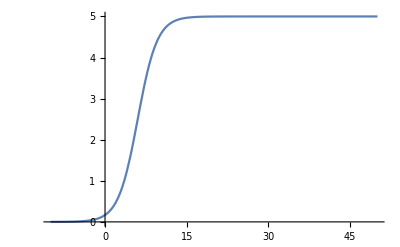

```mathematica
Plot[S[x], {x,-10,50}]
```

```mathematica
S[-5600]
```

0.208232

```mathematica
D[S[u], u]
```

(2.8 ⅇ^(0.56 (6-u)))/((1+ⅇ^(0.56 (6-u)))^2)

```mathematica
system={
x0'[t]==y0[t],
y0'[t]==A*a*S[upy[t]]-2*a*y0[t]-a^2*x0[t],
x1'[t]==y1[t],
y1'[t]==A*a*(1/C2+S[uex[t]])-2*a*y1[t]-a^2*x1[t],
x2'[t]==y2[t],
y2'[t]==B*b*S[uis[t]] -2*b*y2[t]-b^2*x2[t],
x3'[t]==y3[t],
y3'[t]==G*g*S[uif[t]]-2*g*y3[t]-g^2*x3[t],
upy[t]==C2*x1[t]-C4*x2[t]-C7*x3[t],
uex[t]==C1*x0[t],
uis[t]==C3*x0[t],
uif[t]==C5*x0[t]-C6*x2[t]
}
```

{True,((0.01625 s)/(1+ⅇ^(0.56 (6-0.8 C x1+0.25 C x2+0.8 C x3)))-10000 x0-200 y0)[t]==1.625/(1+ⅇ^(0.00056 (3/500-(0.8 C x1-0.25 C x2-0.8 C x3)[t])))-10000 x0[t]-200 y0[t],True,(0.325 (1.25/C+5./(1+ⅇ^(0.56 (6-C x0))))-10000 x1-200 y1)[t]==0.325 (1.25/C+5./(1+ⅇ^(0.00056 (3/500-(C x0)[t]))))-10000 x1[t]-200 y1[t],True,(5.5/(1+ⅇ^(0.56 (6-0.25 C x0)))-2500 x2-100 y2)[t]==5.5/(1+ⅇ^(0.00056 (3/500-(0.25 C x0)[t])))-2500 x2[t]-100 y2[t],True,(25./(1+ⅇ^(0.56 (6-0.3 C x0+0.1 C x2)))-250000 x3-1000 y3)[t]==25./(1+ⅇ^(0.00056 (3/500-(0.3 C x0-0.1 C x2)[t])))-250000 x3[t]-1000 y3[t],(0.8 C x1-0.25 C x2-0.8 C x3)[t]==0.8 C x1[t]-0.25 C x2[t]-0.8 C x3[t],(C x0)[t]==C x0[t],(0.25 C x0)[t]==0.25 C x0[t],(0.3 C x0-0.1 C x2)[t]==0.3 C x0[t]-0.1 C x2[t]}

```mathematica
sol=DSolve[system,{y0,y1},{t}][[1]]
```

{True,((0.01625 s)/(1+ⅇ^(0.56 (6-0.8 C x1+0.25 C x2+0.8 C x3)))-10000 x0-200 y0)[t]==1.625/(1+ⅇ^(0.00056 (3/500-(0.8 C x1-0.25 C x2-0.8 C x3)[t])))-10000 x0[t]-200 y0[t],True,(0.325 (1.25/C+5./(1+ⅇ^(0.56 (6-C x0))))-10000 x1-200 y1)[t]==0.325 (1.25/C+5./(1+ⅇ^(0.00056 (3/500-(C x0)[t]))))-10000 x1[t]-200 y1[t],True,(5.5/(1+ⅇ^(0.56 (6-0.25 C x0)))-2500 x2-100 y2)[t]==5.5/(1+ⅇ^(0.00056 (3/500-(0.25 C x0)[t])))-2500 x2[t]-100 y2[t],True,(25./(1+ⅇ^(0.56 (6-0.3 C x0+0.1 C x2)))-250000 x3-1000 y3)[t]==25./(1+ⅇ^(0.00056 (3/500-(0.3 C x0-0.1 C x2)[t])))-250000 x3[t]-1000 y3[t],(0.8 C x1-0.25 C x2-0.8 C x3)[t]==0.8 C x1[t]-0.25 C x2[t]-0.8 C x3[t],(C x0)[t]==C x0[t],(0.25 C x0)[t]==0.25 C x0[t],(0.3 C x0-0.1 C x2)[t]==0.3 C x0[t]-0.1 C x2[t]}

```mathematica
system/.sol//Simplify//PowerExpand//Simplify
```

{y0[t],1.625/(1+1. ⅇ^(-0.00056 (C (0.8 x1-0.25 x2-0.8 x3))[t]))-10000 x0[t]-200 y0[t],y1[t],0.40625/C+1.625/(1+1. ⅇ^(-0.00056 (C x0)[t]))-10000 x1[t]-200 y1[t],y2[t],5.5/(1+1. ⅇ^(-0.00056 (0.25 C x0)[t]))-2500 x2[t]-100 y2[t],y3[t],25./(1+1. ⅇ^(-0.00056 (0.3 C x0-0.1 C x2)[t]))-250000 x3[t]-1000 y3[t],C (0.8 x1[t]-0.25 x2[t]-0.8 x3[t]),C x0[t],0.25 C x0[t],0.3 C x0[t]-0.1 C x2[t]}/.{y0[t],1.625/(1+1. ⅇ^(-0.00056 (C (0.8 x1-0.25 x2-0.8 x3))[t]))-10000 x0[t]-200 y0[t],y1[t],0.40625/C+1.625/(1+1. ⅇ^(-0.00056 (C x0)[t]))-10000 x1[t]-200 y1[t],y2[t],5.5/(1+1. ⅇ^(-0.00056 (0.25 C x0)[t]))-2500 x2[t]-100 y2[t],y3[t],25./(1+1. ⅇ^(-0.00056 (0.3 C x0-0.1 C x2)[t]))-250000 x3[t]-1000 y3[t],C (0.8 x1[t]-0.25 x2[t]-0.8 x3[t]),C x0[t],0.25 C x0[t],0.3 C x0[t]-0.1 C x2[t]}

```mathematica
system={p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4*q[x]*r[x])};
```

{p'[x]==1,q'[x]==x,True,s'[x]==(0.00056[x])/(p[x]+4 0.00056[x] q[x])}

```mathematica
sol=DSolve[system,{p,q,r,s},x]
```

DSolve[{p'[x]==1,q'[x]==x,True,s'[x]==(0.00056[x])/(p[x]+4 0.00056[x] q[x])},{p,q,0.00056,s},x]

```mathematica
m0=-10;
k=3;
F={r↦1,r↦2,r↦3};
Y=Table[ToExpression["y"<>ToString[i]],{i,1,2 k+1}];
Y0=RandomReal[{-1,1},{2 k+1}];
Y1=RandomReal[{-1,1},{2 k+1}];
t0=0.1;
tmax=2.;
eq=Simplify@Table[Plus[1/r D[1/r D[Y[[m-(m0-k)+1]][r],r],r],-m^2 Y[[m-(m0-k)+1]][r],r^2 Plus[F[[1]][r] Y[[m-(m0-k)+1]][r],If[m-1≥m0-k,F[[2]][r] Y[[m-1-(m0-k)+1]][r],0],If[m-2≥m0-k,F[[3]][r] Y[[m-2-(m0-k)+1]][r],0]]]==0,{m,m0-k,m0+k}];
initeqs=Flatten[Table[{Y[[i]][t0]==Y0[[i]],Y[[i]]'[t0]==Y1[[i]]},{i,1,2 k+1}]];

NDSolve[Join[eq,initeqs],Evaluate[Table[yy[r],{yy,Y}]],{r,t0,tmax}]
```

NDSolve[{1. ∂_0.00056 (1785.71 ∂_0.00056 y1[0.00056])==0.09464 y1[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y2[0.00056])+3.51232×10^-10 y1[0.00056]==0.08064 y2[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y3[0.00056])+5.26848×10^-10 y1[0.00056]+3.51232×10^-10 y2[0.00056]==0.06776 y3[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y4[0.00056])+5.26848×10^-10 y2[0.00056]+3.51232×10^-10 y3[0.00056]==0.056 y4[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y5[0.00056])+5.26848×10^-10 y3[0.00056]+3.51232×10^-10 y4[0.00056]==0.04536 y5[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y6[0.00056])+5.26848×10^-10 y4[0.00056]+3.51232×10^-10 y5[0.00056]==0.03584 y6[0.00056],1. ∂_0.00056 (1785.71 ∂_0.00056 y7[0.00056])+5.26848×10^-10 y5[0.00056]+3.51232×10^-10 y6[0.00056]==0.02744 y7[0.00056],y1[0.1]==0.61174,(0.325 (1.25/C+5./(1+ⅇ^(0.56 (6-C x0))))-10000 x1-200 y1)[0.1]==-0.236549,y2[0.1]==-0.945523,(5.5/(1+ⅇ^(0.56 (6-0.25 C x0)))-2500 x2-100 y2)[0.1]==0.12738,y3[0.1]==-0.652196,(25./(1+ⅇ^(0.56 (6-0.3 C x0+0.1 C x2)))-250000 x3-1000 y3)[0.1]==-0.754195,y4[0.1]==-0.636076,y4'[0.1]==-0.24528,y5[0.1]==-0.114604,y5'[0.1]==0.241859,y6[0.1]==-0.1316,y6'[0.1]==0.807906,y7[0.1]==-0.50992,y7'[0.1]==-0.781587},{y1[0.00056],y2[0.00056],y3[0.00056],y4[0.00056],y5[0.00056],y6[0.00056],y7[0.00056]},{0.00056,0.1,2.}]